```mathematica
outfix=(x+1)x(x-1)(x-4);
D[outfix,x]
Solve[%==0,x]
```

(-4+x) (-1+x) x+(-4+x) (-1+x) (1+x)+(-4+x) x (1+x)+(-1+x) x (1+x)

{{x→Root-0.601Root[2-#1-6 #1^2+2 #1^3&,1]-0.6009558883393541},{x→Root0.544Root[2-#1-6 #1^2+2 #1^3&,2]0.5444105961768785},{x→Root3.06Root[2-#1-6 #1^2+2 #1^3&,3]3.056545292162476}}

```mathematica
Plot[outfix(x-157813627/51631372)^2,{x,-2,5}]
Plot[outfix,{x,-2,5}]
```

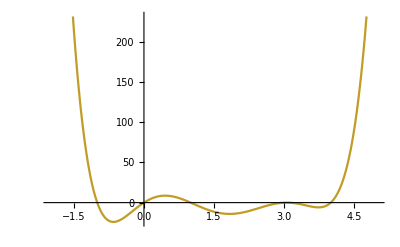

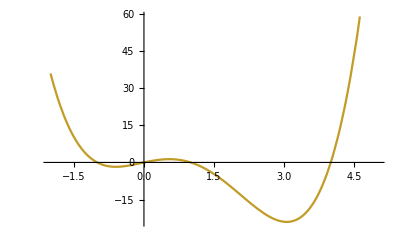

```mathematica
FindMinimum[{outfix,2≤x≤4},x]
```

{-24.0573,{x→3.05655}}

```mathematica
Rationalize[3.056545291881843,0]n
```

157813627/51631372

```mathematica
Reduce[outfix≥0,x]
Reduce[outfix(x-157813627/51631372)^2≥0,x]
```

x≤-1||0≤x≤1||x≥4

x≤-1||0≤x≤1||x==157813627/51631372||x≥4

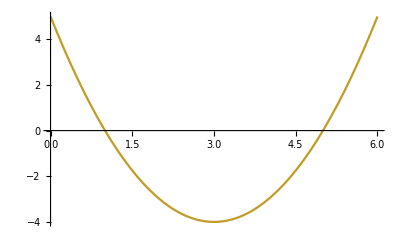

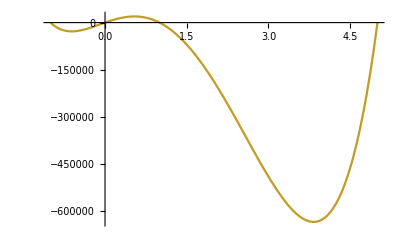

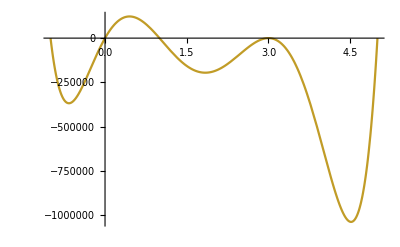

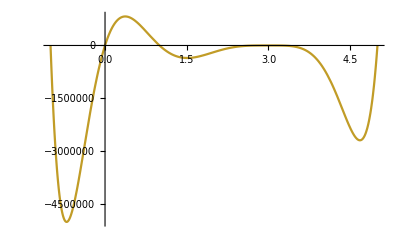

```mathematica
Plot[(x-1)(x-5),{x,0,6}]
Plot[(x+1)x(x-1)((x-2)^2+100)((x-4)^2+100)(x-5),{x,-1,5}]
(*It's not enough to `cancel` with local minimum*)
Plot[(x+1)x(x-1)((x-2)^2+100)(x-3)^2((x-4)^2+100)(x-5),{x,-1,5}]
Plot[(x+1)x(x-1)((x-2)^2+100)(x-3)^4((x-4)^2+100)(x-5),{x,-1,5}]
```

```mathematica
Plot[(x-1)(x-5),{x,0,6}]
Reduce[(x+1)x(x-1)((x-2)^2+100)((x-4)^2+100)(x-5)≥0,x]
(*It's not enough to `cancel` with local minimum (with a exponent of 2 ...)*)
Reduce[(x+1)x(x-1)((x-2)^2+100)(x-3)^2((x-4)^2+100)(x-5)≥0,x]
Reduce[(x+1)x(x-1)((x-2)^2+100)(x-3)^4((x-4)^2+100)(x-5)≥0,x]
```

-Graphics-

x≤-1||0≤x≤1||x≥5

x≤-1||0≤x≤1||x==3||x≥5

x≤-1||0≤x≤1||x==3||x≥5